# Legendre Polynomials

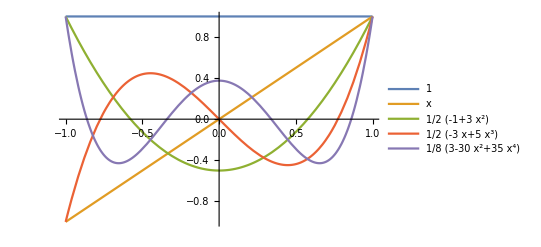

```mathematica
Plot[Evaluate[Table[LegendreP[n,x],{n,0,4}]],{x,-1,1},PlotLegends->"Expressions"]
```

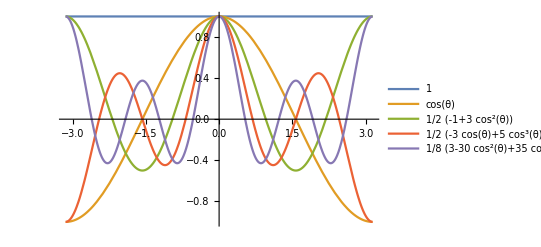

```mathematica
Plot[Evaluate[Table[LegendreP[n,Cos[θ]],{n,0,4}]],{θ,-π,π},PlotLegends->"Expressions"]
```

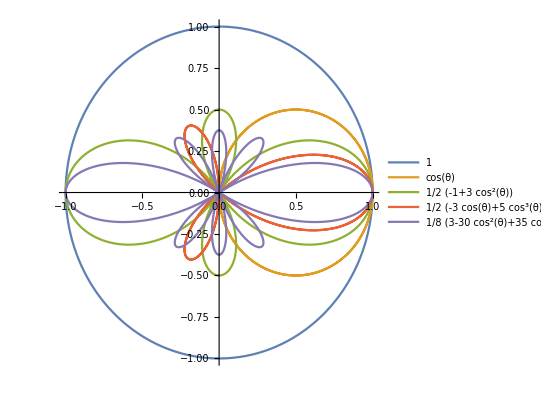

```mathematica
PolarPlot[Evaluate[Table[LegendreP[n,Cos[θ]],{n,0,4}]],{θ,-π,π},PlotLegends->"Expressions"]
```

```mathematica
Table[Integrate[LegendreP[m,x]LegendreP[n,x],{x,-1,1}](n+1/2),{m,0,4},{n,0,4}];
MatrixForm[%]
```

(1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)